```mathematica
dir=NotebookDirectory[];
SetDirectory[dir];
```

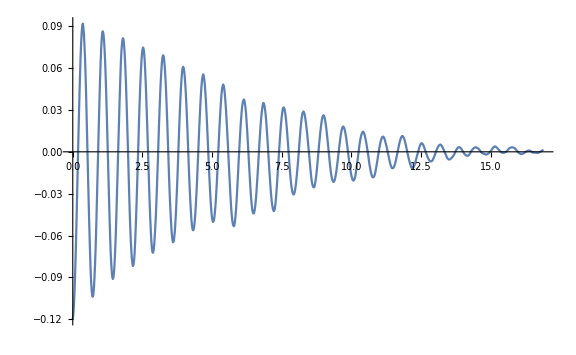

```mathematica
swingphi = Flatten@Import["/Users/morbo/stuffs/mathematica_analysis/swingphi.mat","Data"];
data=Take[swingphi,{155,Length@swingphi}];
sdata = MapAt[(#)+0.062&,data,All];
fdata = Table[{(i-1) 20 10^-3,sdata[[i]]},{i,1,Length@data}];
ListLinePlot[fdata,ImageSize->Large]
Δt = fdata[[2,1]]-fdata[[1,1]];
timestart = fdata[[1,1]];
timestop = fdata[[Length[data],1]];
```

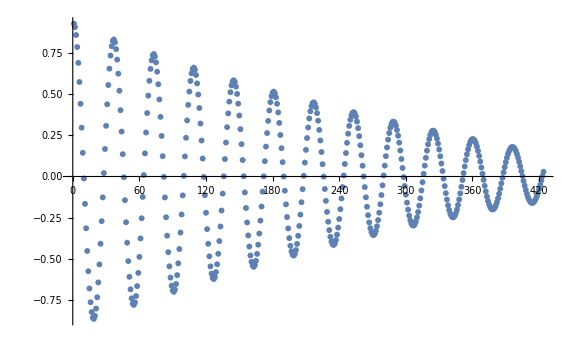

```mathematica
corrdata = Table[fdata[[i,2]], {i,1,Length[fdata]}];
corr=ListCorrelate[Take[corrdata,Quotient[Length[corrdata],2]],corrdata];
ListPlot[corr,ImageSize->Large]
```

```mathematica
gaps=Length/@Rest@Most@Split[UnitStep@Differences[corr],#1≤#2&];
per = Mean[N[gaps]] Δt;
params = {mb->(1.617-0.124),mw->0.124,l->0.097,g->9.81, k -> 0.106,jw -> 0.00028331372879321354};
inertia=𝒿 /. First[Solve[{((mb l+mw k) g)/(𝒿 + jw)==(2π 1/per)^2},𝒿] /. params];
Solve[√((g( mb l + mw k ))/(𝒿 + jw)) == 2 π/per,𝒿] /. params
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::nongen: Solutions may not be valid for all values of parameters.

{{𝒿→0.0199524}}

```mathematica
fa=2/(√(Length@fdata[[All,2]]))Abs@Fourier[fdata[[All,2]]];
peaksize= Last[TakeLargest[fa,2]];
peaks= Flatten[Position[fa,x_ /; x≥ peaksize]];
pos = First[peaks];
n = Length@fdata[[All,2]];
```

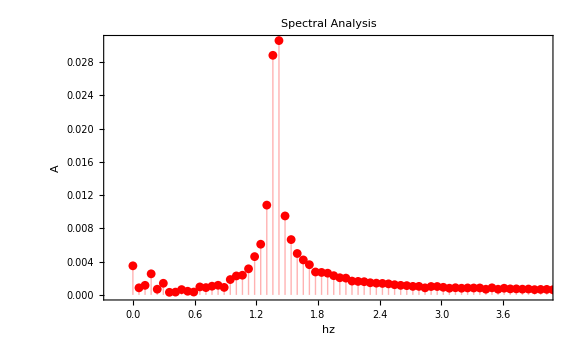

```mathematica
ListPlot[fa,Filling->Axis,DataRange->{0,(n-1)/Last@fdata[[All,1]]}, PlotRange->{{-0.2,4},All},PlotStyle->{{Red,PointSize[0.011]}},ImageSize->Large, PlotLabel->"Spectral Analysis",FrameLabel->{"hz","A"},Frame -> True, FrameStyle->Black]
```

```mathematica
fr = Abs[Fourier[fdata Exp[2 Pi I (pos - 2) N[Range[0, n - 1]]/n], FourierParameters->{0,2/n}]];
frpos = Position[fr, Max[fr]][[1,1]];
period=N[n/(pos - 2 + 2 (frpos - 1)/n)] Δt;
Solve[√((g( mb l + mw k ))/(𝒿 + jw))== 2 π/T,l] /. {T -> period, mb->(1.617-0.124),mw->0.124,g->9.81, k -> 0.106,jw -> 0.00028331372879321354,𝒿->0.019952423487442736}
```

Solve::nongen: Solutions may not be valid for all values of parameters.

{{l→0.0992796}}

```mathematica
physpendulum =ParametricNDSolveValue[{(Θ+jw) x''[t]+ (mb l+mw k) g  Sin[x[t]]==-μ(Tanh[x'[t]/0.1])- rb x'[t]/. params,x[0]==fdata[[1,2]],x'[0]==0 },x,{t,timestop+1},{μ,Θ,rb}];
```

```mathematica
Manipulate[Plot[#[t]& @ physpendulum[μ,Θ,rb] ,{t,0,timestop+1},Epilog->{Red,Point[fdata]},ImageSize->{GoldenRatio 600,600},PlotPoints-> 50,PlotRange->{{0,timestop+1},{-0.11,0.11}},PlotPoints->200, Frame->True, FrameStyle->Black],{{μ,0.0001},1 10^-5,1 10^-3,Appearance -> "Labeled"},{{Θ,inertia},inertia-inertia/2,5*(inertia),Appearance -> "Labeled"},{{rb,0.00804},1 10^-5,1 10^-1,Appearance -> "Labeled"}]
```

```mathematica
nmodel[𝒿_?NumberQ,μ_?NumberQ,rb_?NumberQ] :=  (nmodel[𝒿,μ,rb]=Module[{x,t},First[x/.NDSolve[{(𝒿+jw) x''[t]+ (mb l+mw k) g  Sin[x[t]]==-μ(ArcTan[x'[t]/0.1])- rb x'[t]/. {mb->1.617-0.124,mw->0.124,g->9.81, k -> 0.106, l -> l->0.09927955263574209, jw -> 0.00028331372879321354},x[0]==fdata[[1,2]],x'[0]==0 },x,{t,0,Last@fdata[[All,1]]}]]])
```

```mathematica
nfit=NonlinearModelFit[fdata,nmodel[𝒿,μ,rb][t],{{𝒿,0.019},{μ,0.0001},{rb,0.00080497}},t,Method->"Gradient"]
nfit["BestFitParameters"]
```

FittedModel[InterpolatingFunction[…][t]]

{𝒿→0.020052,μ→0.000492963,rb→0.00594164}

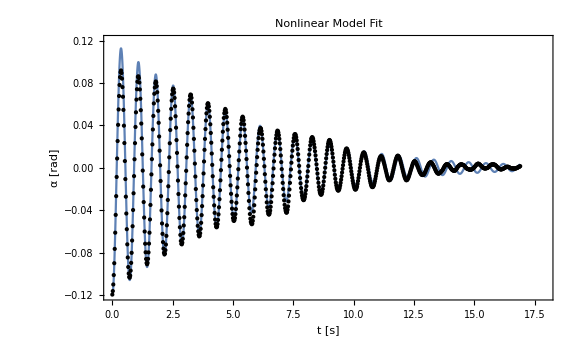

```mathematica
Plot[{nfit[t]},{t,0,Last@fdata[[All,1]]},Epilog-> {Black,Point[fdata]},PlotPoints-> 50,PlotRange->{{0,timestop+1},{-0.12,0.12}},PlotPoints->200, Frame->True, FrameStyle->Black,PlotLabel->"Nonlinear Model Fit", FrameLabel->{"t [s]","α [rad]"},ImageSize->Large]
```